```mathematica
spec[list_List]:=Total@list+Length@list-1;(*上文中使得数组合法的指标*)
geneList[list_List,n_Integer]:=Module[{m},m=n-spec[list]-1;If[m>=1,Table[Append[list,i],{i,m}],None]]
(*generate list函数,对每个数组都能用此衍生出一个列表的合法数组,通过在原数组后加数字*)
eligibleListFunc[n_Integer]:=Module[{eligibleTree,eligibleList={}},
eligibleTree=NestTree[geneList[#,n]&,{},Infinity];(*从空列表开始把上述数组作为子树*)
TreeFold[{AppendTo[eligibleList,#1]&,AppendTo[eligibleList,#]&},eligibleTree];eligibleList
(*把树转换为列表，其中保留空数组，最终得到的列表在eligibleList中,eligibleList包含所有在单行n格下所有可行的数组*)];
```

```mathematica
whiteGridSolution[cspec_Integer,len_Integer]:=Module[{solutionList},solutionList=IntegerPartitions[cspec,len+1];solutionList=Flatten[Permutations@PadRight[#,len+1]&/@solutionList,1];solutionList[[All,{1,-1}]]=solutionList[[All,{1,-1}]]-1;solutionList+1]
(*给定Nonogram中的标黑格子数组，给出所有标白格子的方案。使用了IntegerPartitions来给出所有方案。*)
blackGridGivenList[blist_List,wlist_List]:=
Module[{returnList={},len=Length@blist},
Do[AppendTo[returnList,{ConstantArray[0,wlist[[k]]],ConstantArray[1,blist[[k]]]}],{k,len}];
AppendTo[returnList,ConstantArray[0,wlist[[len+1]]]];Flatten@returnList];
(*给定标黑格子数组和标白格子数组，给出按1和0表示的单行格子数组。仅仅是交互输出*)
blackGridProbability[list_List,n_Integer]:=Module[{cspec=n-spec@list,len=Length@list,solutionList,solutionNumber},
solutionList=whiteGridSolution[cspec,len];solutionNumber=Length@solutionList;Total[blackGridGivenList[list,#]&/@solutionList]/solutionNumber]
(*能给出每个列表对应格子中标黑的概率是多少。*)
eligibleProbListFunc[n_Integer]:=(#->blackGridProbability[#,n]&/@eligibleListFunc[n])
```

```mathematica
blackProbVisible=#[[1]]->Grid[{(If[0<#<1,N[#,2]," "]&)/@#[[2]]},Frame->All,Background->{(If[#==1,Black,White]&)/@#[[2]]}]&;
```

```mathematica
blackProbVisible/@eligibleProbListFunc[10](*输入单行格子数量*)
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.015625,0.03125,0.046875,0.0625,0.171875,0.109375,0.390625,0.71875,1.375,3.0625,5.98438,13.25}

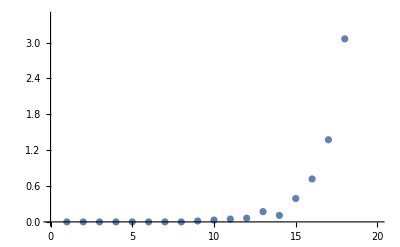

```mathematica
Table[Timing[blackProbVisible/@eligibleProbListFunc[n];][[1]],{n,20}]
ListPlot[%]
```